```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;Clear[κ,κi,κr];rep={a2->Subscript[b, 1],a1->Subscript[a, 1],κi->Subscript[κ, i],κr->Subscript[κ, r], ky->Subscript[k, y], kz->Subscript[k, z],en->e};
ass=Assumptions->{v,k,kx,ky,kz,κi,κr,a1,a2,a,b,η}∈ Reals && -1<η<1;
sx=({{0, 1}, {1, 0}});sy=({{0, -ⅈ}, {ⅈ, 0}});sz=({{1, 0}, {0, -1}});
id=({{1, 0}, {0, 1}});{dx,dy,dz}={ kx, ky,kz};
```

## Untilted: x=0 surface

```mathematica
kx sxψ+ky syψ+kz szψ/.kx->-ⅈ Dx
```

-ⅈ Dx sxψ+ky syψ+kz szψ

```mathematica
Clear[ψ,eq0,eq,eqn,a1,a2,κ,κr,κi];κ=κr+ⅈ κi;
ψ={1,a1+ⅈ a2};
ψdag={1,a1-ⅈ a2};
prod=FullSimplify[ψdag.(sx.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
```

{2 a1,0}

```mathematica
a1=0;ψ={1,a1+ⅈ a2};
eq=2FullSimplify[ⅈ κ sx.ψ+ky sy.ψ+kz sz.ψ-en id.ψ,ass]
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[ eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0  && κr≠0,{en,κr,κi,a2}],ass]
Clear[κi,a1,a2,en];
```

{2 (-en+kz+a2 (ky-ⅈ κi-κr)),2 ⅈ (ky-a2 (en+kz)+ⅈ κi+κr)}

{2 (-en+kz+a2 (ky-κr)),-2 a2 κi,-2 κi,2 (ky-a2 (en+kz)+κr)}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→(2 a2 ky+kz-a2^2 kz)/(1+a2^2),κr→((-1+a2^2) ky+2 a2 kz)/(1+a2^2),κi→0}}

```mathematica
(* where do κr goes to zero and mixes with the bulk states? *)bulkentry=FullSimplify[Solve[(2 a2 ky+(1-a2^2 )kz)/(1+a2^2)==μ && √(kz^2+ky^2)==μ,{ky,kz}],ass]//Flatten
FullSimplify[(* κr = *)((-1+a2^2) ky+2 a2 kz)/(1+a2^2)/.bulkentry,ass]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ky→(2 a2 μ)/(1+a2^2),kz→(μ-a2^2 μ)/(1+a2^2)}

0

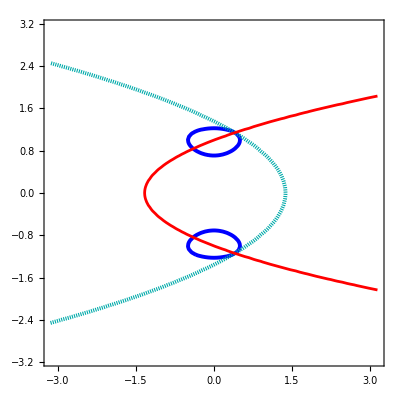

```mathematica
(* where do κr goes to zero? *)
lim=π;th=0.007;mu=0.5;kw=1;kzfac=(*kz*)(kz^2-kw^2);
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
a2v={0.5,2};
(*********)
a2=a2v[[1]];
c1=ContourPlot[(2 a2 ky+(1-a2^2 )kzfac)/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[1]],RegionFunction->Function[{ky,kz,z},Chop[(-1+a2^2) ky+2 a2 kzfac]>=0 ],PlotLegends->Automatic]//Quiet;
κ1=ContourPlot[((-1+a2^2) ky+2 a2 kzfac)/(1+a2^2)==0(* where κr fors to zero *),{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red,PlotLegends->Automatic]//Quiet;
kx=0;fs=ContourPlot[kzfac^2+kx^2+ky^2==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Blue,Thickness[th]],PlotLegends->Automatic];
Show[fs,c1,κ1]
Clear[a2,kx,kzfac,kw]
```

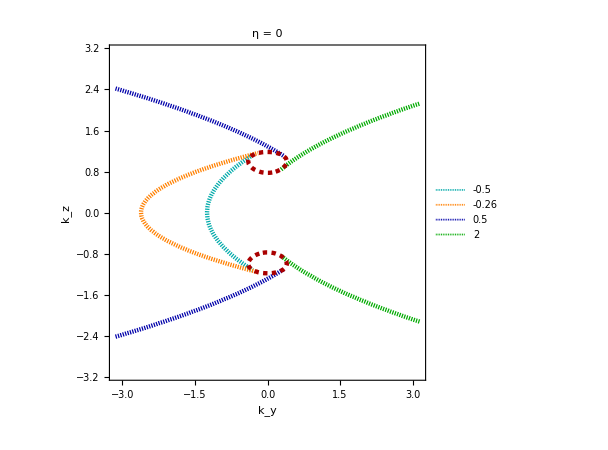

```mathematica
(* 2 nodes *)
lim=π;mu=0.4;kw=1;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
a2v={-0.5,-0.26,0.5,2};
(*********)
a2=a2v[[1]];
c1=ContourPlot[(2 a2 ky+(kz^2-kw^2)-a2^2 (kz^2-kw^2))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[1]],RegionFunction->Function[{ky,kz,z},Chop[((-1+a2^2) ky+2 a2 (kz^2-kw^2))/(1+a2^2)]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
a2=a2v[[2]];
c2=ContourPlot[(2 a2 ky+(kz^2-kw^2)-a2^2 (kz^2-kw^2))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[2]],RegionFunction->Function[{ky,kz,z},Chop[((-1+a2^2) ky+2 a2 (kz^2-kw^2))/(1+a2^2)]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
a2=a2v[[3]];
c3=ContourPlot[(2 a2 ky+(kz^2-kw^2)-a2^2 (kz^2-kw^2))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[3]],RegionFunction->Function[{ky,kz,z},Chop[((-1+a2^2) ky+2 a2 (kz^2-kw^2))/(1+a2^2)]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
a2=a2v[[4]];
c4=ContourPlot[(2 a2 ky+(kz^2-kw^2)-a2^2 (kz^2-kw^2))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[4]],RegionFunction->Function[{ky,kz,z},Chop[((-1+a2^2) ky+2 a2 (kz^2-kw^2))/(1+a2^2)]>=0 ],PlotLegends->Automatic]//Quiet;
(***************)
kx=0;fs=ContourPlot[(kz^2-kw^2)^2+kx^2+ky^2==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]],PlotLegends->Automatic];
pl1=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"η = 0",20,FontFamily->"TexMaths Symbols",Brown,Bold](**)];
leg=LineLegend[style,{a2v[[1]], a2v[[2]], a2v[[3]], a2v[[4]]},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
plt=Legended[Graphics[pl1],Placed[leg,Below]]
Clear[kx,mu,kw,a2];
SetDirectory[NotebookDirectory[]];
(*Export["weylarc.pdf",Rasterize[plt],ImageResolution->100];*)
```

## Tilted case

### dispersion

```mathematica
Eigenvalues[kx sx+ky sy+kz sz+kx η id]
```

{-√(kx^2+ky^2+kz^2)+kx η,√(kx^2+ky^2+kz^2)+kx η}

```mathematica
(* maximum-radii FS-projections: *)
Solve[D[√(kx^2+ky^2+kz^2)+kx η,kx]==0,kx]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kx→-(ⅈ √(ky^2+kz^2) η)/(√(-1+η^2))},{kx→(ⅈ √(ky^2+kz^2) η)/(√(-1+η^2))}}

```mathematica
eta=0.7;lim=1.3;mu=0.4;kx=0;Plot3D[{√((kz)^2+kx^2+ky^2)+kx eta,-√((kz)^2+kx^2+ky^2)+kx eta},{ky,-lim,lim},{kz,-lim,lim},PlotRange->{-1,1},BoxRatios->{0.75, 0.75, 1}];
kx=-(√(ky^2+kz^2) eta)/(√(1-eta^2));Plot3D[{√((kz)^2+kx^2+ky^2)+kx eta,-√((kz)^2+kx^2+ky^2)+kx eta},{ky,-lim,lim},{kz,-lim,lim},PlotRange->{-1,1},BoxRatios->{0.75, 0.75, 1}];
ContourPlot3D[{kz^2+kx^2+ky^2==(mu-kx eta)^2,kx==-(√(ky^2+kz^2) eta)/(√(1-eta^2))},{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},AxesLabel->{kx,ky,kz}]
Clear[kx,eta];
```

-Graphics3D-

```mathematica
FullSimplify[√(kz^2+kx^2+ky^2)+kx η/.kx->- √((ky^2+kz^2)/(1-η^2)) η,ass]
```

-√((ky^2+kz^2)/(1-η^2)) (-1+η^2)

### single tilted node

```mathematica
kx η idψ+kx sxψ+ky syψ+kz szψ/.kx->-ⅈ Dx
```

-ⅈ Dx sxψ+ky syψ+kz szψ-ⅈ Dx idψ η

```mathematica
Clear[ψ,eq0,eq,eqn,a1,a2,κ,κr,κi,η];κ=κr+ⅈ κi;
ψ={1,a1+ⅈ a2};
ψdag={1,a1-ⅈ a2};
prod=FullSimplify[ψdag.(sx.ψ)+ψdag.ψ η,ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
```

{2 a1+(1+a1^2+a2^2) η,0}

```mathematica
ψ={1,a1+ⅈ a2};
eq=FullSimplify[ⅈ κ η id.ψ+ⅈ κ sx.ψ+ky sy.ψ+kz sz.ψ-en id.ψ,ass]
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[ 2 a1+(1+a1^2+a2^2) η==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0  && κr≠0,{en,κr,κi,a1}],ass]
Clear[κi,κ,κr,a1,a2,en];
```

{-en-ⅈ a1 ky+a2 ky+kz-a1 κi-ⅈ a2 κi-η κi+ⅈ (a1+ⅈ a2+η) κr,-((a1+ⅈ a2) (en+kz+η (κi-ⅈ κr)))+ⅈ (ky+ⅈ κi+κr)}

{-en+kz-(a1+η) κi+a2 (ky-κr),-a1 ky-a2 κi+(a1+η) κr,-κi-a1 (en+kz+η κi)-a2 η κr,ky-a2 (en+kz+η κi)+κr+a1 η κr}

{{en→(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2),κr→(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2)),κi→(η (a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (-1+√(1-(1+a2^2) η^2))))/((1+a2^2) (-1+η^2)),a1→-(1+√(1-(1+a2^2) η^2))/η},{en→(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2),κr→(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2)),κi→(η (a2^2 kz-kz √(1-(1+a2^2) η^2)-a2 ky (1+√(1-(1+a2^2) η^2))))/((1+a2^2) (-1+η^2)),a1→(-1+√(1-(1+a2^2) η^2))/η}}

```mathematica
(* where κr vanishes, what is the energy value? 
{en->(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2),κr->(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))}*)
Clear[a2val];a2val=Flatten[FullSimplify[Solve[0==-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)) ,a2],ass],1]

η=0;
FullSimplify[(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)/.a2val[[1]],ass]
Clear[η,kx,ky,kz];(* correct soln for μ>0 *)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{a2→(ky kz (-1+η^2)-√((ky^2+kz^2) (1-η^2)) Abs[ky])/(ky^2+kz^2 η^2),a2→(ky kz (-1+η^2)+√((ky^2+kz^2) (1-η^2)) Abs[ky])/(ky^2+kz^2 η^2)}

Piecewise[{{√(ky^2+kz^2), ky<0}, {-√(ky^2+kz^2), True}}]

```mathematica
(* where κr vanishes, what is the energy value?
{en->(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2),κr->(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2))} *)
a2val=Flatten[FullSimplify[Solve[0==-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2) ,a2],ass],1]
η=0;

Simplify[(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2)(*-√(kz^2+ky^2)√(1-η^2)*)/.a2val[[3]],ass]
Simplify[(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2)(*-√(kz^2+ky^2)√(1-η^2)*)/.a2val[[4]],ass]
(* correct solution for μ<0 *)
Clear[η,kx,ky,kz];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{a2→-ⅈ,a2→ⅈ,a2→(ky kz (-1+η^2)-√((ky^2+kz^2) (1-η^2)) Abs[ky])/(ky^2+kz^2 η^2),a2→(ky kz (-1+η^2)+√((ky^2+kz^2) (1-η^2)) Abs[ky])/(ky^2+kz^2 η^2)}

-kz

-kz

```mathematica
(* where does κr go to zero and mixes with the bulk states? 
{en->(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2),κr->(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))}*)
Clear[bulkentry];bulkentry=DeleteDuplicates[FullSimplify[Solve[((-a2^2+√(1-(1+a2^2) η^2))kz+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==μ && √((kz^2+ky^2)(1-η^2))==μ,{ky,kz}],ass]]
FullSimplify[(* κr = *)(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))/.bulkentry,ass]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ky→-(a2 (1+√(1-(1+a2^2) η^2)) μ)/((1+a2^2) (-1+η^2)),kz→((a2^2-√(1-(1+a2^2) η^2)) μ)/((1+a2^2) (-1+η^2))}}

{0}

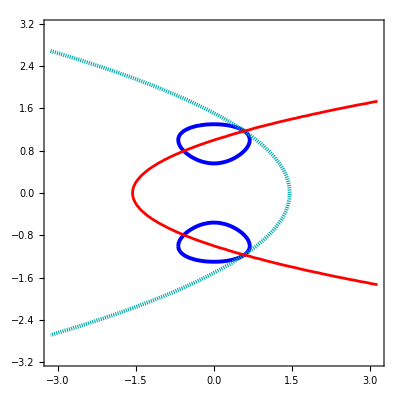

```mathematica
(* where does κr go to zero? *)
lim=π;th=0.007;η=0.49;mu=0.6;kw=1;kzfac=(*kz*)(kz^2-kw^2);
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
a2v={0.5,2};
(*********)
a2=a2v[[1]];
c1=ContourPlot[((-a2^2+√(1-(1+a2^2) η^2))kzfac+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[1]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kzfac (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
κ1=ContourPlot[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kzfac (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))==0(* where κr fors to zero *),{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red,PlotLegends->Automatic]//Quiet;
kx=0;fs=ContourPlot[(kzfac^2+kx^2+ky^2)(1-η^2)==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Blue,Thickness[th]],PlotLegends->Automatic];
Show[fs,c1,κ1]
Clear[a2,kx,kzfac,kw,η]
```

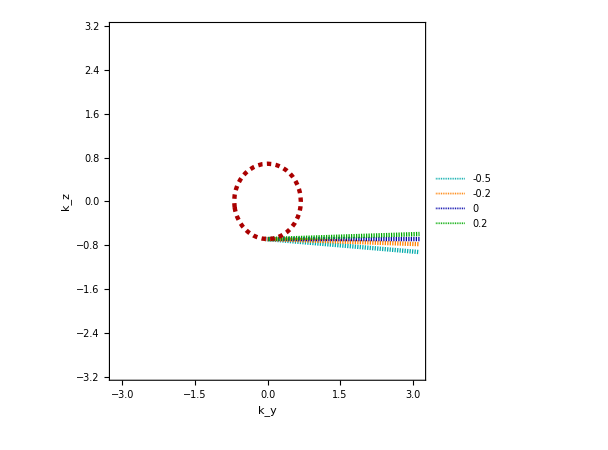

```mathematica
lim=π;mu=0.6;kw=1;η=0.49;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
a2v={-0.5,-0.2,0,0.2};
(*******{en->(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2),κr->(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2))} **********)
i=1;a2=a2v[[i]];
c1=ContourPlot[(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
i=2;a2=a2v[[i]];
c2=ContourPlot[(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
i=3;a2=a2v[[i]];
c3=ContourPlot[(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(***************)
i=4;a2=a2v[[i]];
c4=ContourPlot[(-a2^2 kz-kz √(1-(1+a2^2) η^2)+a2 (ky-ky √(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2 (a2 ky+kz)-ky √(1-(1+a2^2) η^2)+a2 kz √(1-(1+a2^2) η^2))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
kx=(*-(√(ky^2+kz^2) η)/(√(1-η^2))*)0;fs=ContourPlot[(kz^2+kx^2+ky^2)(1-η^2)==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]],PlotLegends->Automatic];

pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450];

plt=Legended[Graphics[pl],Placed[leg,Below]]
Clear[kx,mu,kw,a2,η];
```

### Plot

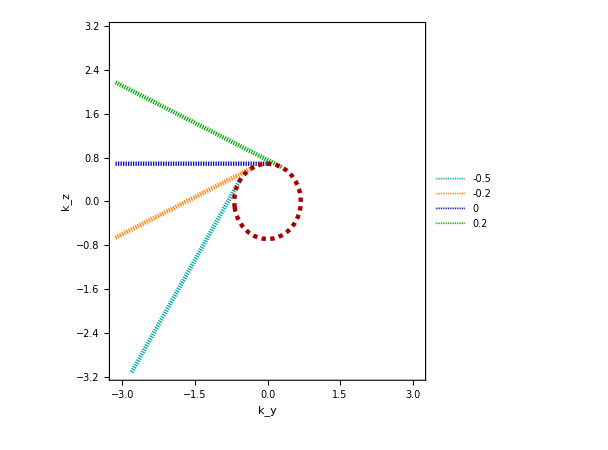

```mathematica
lim=π;mu=0.6;kw=1;η=0.49;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
a2v={-0.5,-0.2,0,0.2};
(*******{en->(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2), κr->(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))} **********)
i=1;a2=a2v[[i]];
c1=ContourPlot[(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
i=2;a2=a2v[[i]];
c2=ContourPlot[(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
i=3;a2=a2v[[i]];
c3=ContourPlot[(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(***************)
i=4;a2=a2v[[i]];
c4=ContourPlot[(-a2^2 kz+kz √(1-(1+a2^2) η^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
kx=(*-(√(ky^2+kz^2) η)/(√(1-η^2))*)0;fs=ContourPlot[(kz^2+kx^2+ky^2)(1-η^2)==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];

pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450];
leg=LineLegend[style,{a2v[[1]], a2v[[2]], a2v[[3]], a2v[[4]]},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

(**********)

(*rp=RegionPlot[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 kz (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))>=0,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz}];
Show[rp,fs]*)
plt=Legended[Graphics[pl],Placed[leg,Below]]
Clear[kx,mu,kw,a2,η];
```

### 2 tilted nodes

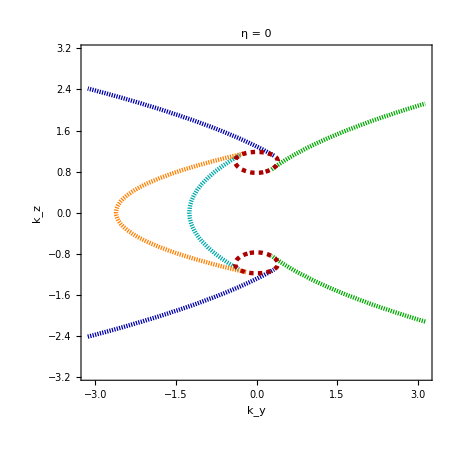
```mathematica
lim=π;mu=0.4;kw=1;η=0.35;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Dashing[0.002]],(**)Directive[Orange,Thickness[th],Dashing[0.002]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.002]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};
(*a2v={-0.5,-0.2,0.2,0.5};*)
a2v={-0.5,-0.26,0.5,2};
(**************************************************************)
a2=a2v[[1]];
c1=ContourPlot[((-a2^2+ √(1-(1+a2^2) η^2)) (kz^2-kw^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[1]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 (kz^2-kw^2) (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
a2=a2v[[2]];
c2=ContourPlot[((-a2^2+ √(1-(1+a2^2) η^2)) (kz^2-kw^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[2]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 (kz^2-kw^2) (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
a2=a2v[[3]];
c3=ContourPlot[((-a2^2+ √(1-(1+a2^2) η^2)) (kz^2-kw^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[3]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 (kz^2-kw^2) (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(*********)
a2=a2v[[4]];
c4=ContourPlot[((-a2^2+ √(1-(1+a2^2) η^2)) (kz^2-kw^2)+a2 ky (1+√(1-(1+a2^2) η^2)))/(1+a2^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->style[[4]],RegionFunction->Function[{ky,kz,z},Chop[(-a2^2 ky+ky √(1-(1+a2^2) η^2)-a2 (kz^2-kw^2) (1+√(1-(1+a2^2) η^2)))/((1+a2^2) (-1+η^2))]>=0 ],PlotLegends->Automatic]//Quiet;
(***************)
kx=-(√(ky^2+(kz^2-kw^2)^2) η)/(√(1-η^2));fs=ContourPlot[(kz^2-kw^2)^2+kx^2+ky^2==(mu-kx η)^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];

pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"η = 0.35",20,FontFamily->"TexMaths Symbols",Brown,Bold](**)];
leg=LineLegend[style,{a2v[[1]], a2v[[2]], a2v[[3]], a2v[[4]]},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl1=-Graphics-;

plt=Legended[GraphicsGrid[{{pl1,pl}},ImageSize->900],Placed[leg,Below]]
Clear[kx,mu,kw,a2,η];
SetDirectory[NotebookDirectory[]];
Export["weylarc.pdf",Rasterize[plt],ImageResolution->200];
```

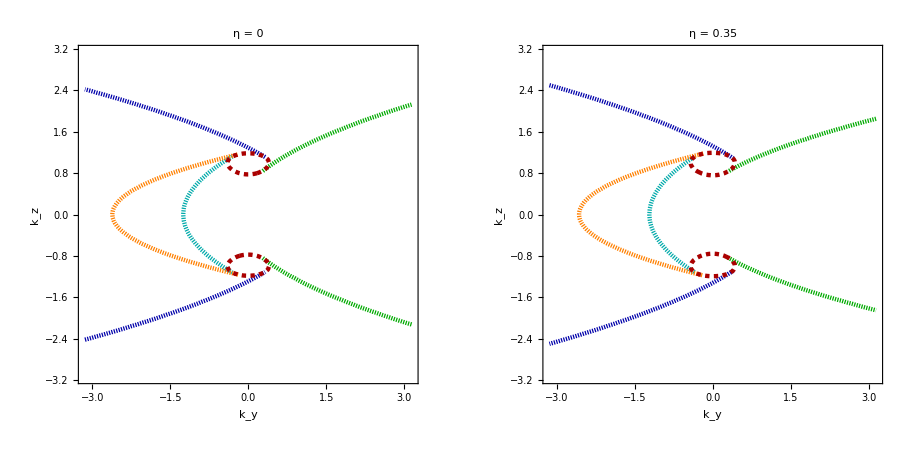

## z=0 surface for 2 nodes

```mathematica
kx sxψ+ky syψ+(kz^2-kw^2) szψ/.kz->-ⅈ Dz
```

kx sxψ+ky syψ+(-Dz^2-kw^2) szψ

```mathematica
Clear[ψ,eq0,eq,eqn,a1,a2,,κ,κr,κi,b1,b2,α];κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ a2};
ψdag={1,a1-ⅈ a2};
prod=2 κi FullSimplify[ψdag.(sz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
```

Clear::wrsym: Symbol Null is Protected.

{0,0}

```mathematica
eq=2FullSimplify[kx sx.ψ+ky sy.ψ+(-κ^2-kw^2) sz.ψ-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[ eqn[[1]]==0 && eqn[[2]]==0 (*&& eqn[[4]]==0 &&*)  && κr≠0,{en,a1}],ass]
FullSimplify[{ky^2 eqn[[3]]/2, eqn[[4]]/2}/.solu]
Clear[κi,a1,a2,en];
```

{-2 (en+kw^2-a1 kx-a2 ky+κr^2),2 a2 kx-2 a1 ky,2 (kx+a1 (-en+kw^2+κr^2)),2 (ky+a2 (-en+kw^2+κr^2))}

{{en→-kw^2+a2 (kx^2/ky+ky)-κr^2,a1→(a2 kx)/ky}}

{{kx ky (ky-(a2^2 (kx^2+ky^2))/ky+2 a2 (kw^2+κr^2)),ky-(a2^2 (kx^2+ky^2))/ky+2 a2 (kw^2+κr^2)}}

```mathematica
en=-kw^2+a2 (kx^2/ky+ky)-κr^2;a1=(a2 kx)/ky;
sol=FullSimplify[Solve[ky-(a2^2 (kx^2+ky^2))/ky+2 a2 (kw^2+κr^2)==0,κr]]
FullSimplify[{-kw^2+a2 (kx^2/ky+ky)-κr^2,κr}/.sol]
Clear[en,a1]
```

{{κr→-(√(-2 a2 kw^2 ky-ky^2+a2^2 (kx^2+ky^2)))/(√2 √a2 √ky)},{κr→(√(-2 a2 kw^2 ky-ky^2+a2^2 (kx^2+ky^2)))/(√2 √a2 √ky)}}

{{ky/(2 a2)+(a2 (kx^2+ky^2))/(2 ky),-(√(-2 a2 kw^2 ky-ky^2+a2^2 (kx^2+ky^2)))/(√2 √a2 √ky)},{ky/(2 a2)+(a2 (kx^2+ky^2))/(2 ky),(√(-2 a2 kw^2 ky-ky^2+a2^2 (kx^2+ky^2)))/(√2 √a2 √ky)}}

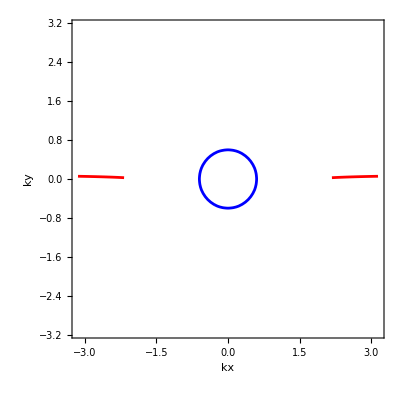

```mathematica
(* 2 nodes *)
lim=π;a2=1;mu=0.6;kw=1;
c1=ContourPlot[ky/(2 a2)+(a2 (kx^2+ky^2))/(2 ky)==mu,{kx,-lim,lim},{ky,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red,RegionFunction->Function[{kx,ky,z},Chop[(√(-2 a2 kw^2 ky-ky^2+a2^2 (kx^2+ky^2)))/(√2 √a2 √ky)]>=0 && Abs[Im[(√(-2 a2 kw^2 ky-ky^2+a2^2 (kx^2+ky^2)))/(√2 √a2 √ky)]]<1.0/100],PlotLegends->Automatic]//Quiet;
kz=kw;fs=ContourPlot[(kz^2-kw^2)^2 0+kx^2+ky^2==mu^2,{kx,-lim,lim},{ky,-lim,lim},ContourStyle->Blue,PlotLegends->Automatic];
Show[c1,fs,FrameLabel->{kx,ky}]
Clear[kz,mu,kw,κi];
```